```mathematica
η=.14;

Ωp[n_,m_,η_]:=Exp[-η^2/2] √((nMin!)/(nMax!))η^(nMax-nMin)LaguerreL[nMin,nMax-nMin,η^2]/.nMin->Min[m,n]/.nMax->Max[m,n];
carriers={#,Ωp[#,#,η]}&/@Range[0,10];
sb1={#,Ωp[#,#+1,η]}&/@Range[0,10];
```

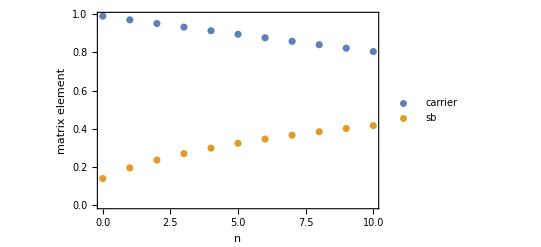

```mathematica
ListPlot[{carriers,sb1},Axes->False,Frame->True,FrameLabel->{"n","matrix element"},LabelStyle->{Black,17},PlotLegends->{"carrier","sb"}]
```